```mathematica
Integrate[2x-5,{x,3,4}]+Integrate[4,{x,4,5}]+Integrate[-4x+24,{x,5,6}]
```

8

```mathematica
?Piecewise
```

Piecewise[{{val_1,cond_1},{val_2,cond_2},…}] represents a piecewise function with values val_i in the regions defined by the conditions cond_i. 
Piecewise[{{val_1,cond_1},…},val] uses default value val if none of the cond_i apply. The default for val is 0.

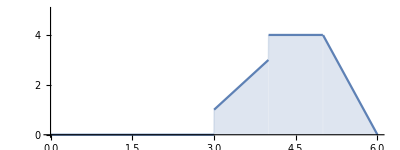

```mathematica
plot=Plot[Piecewise[{
{2x-5,3≤x≤4},
{4,4≤x≤5},
{-4x+24,5≤x≤6}
},0],{x,0,6},Filling->Axis,AspectRatio->0.375,PlotRange->{0,5}]
```

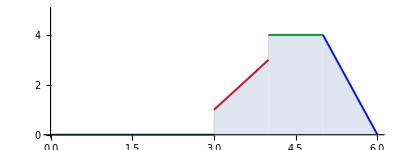

```mathematica
Show[{
plot,
Graphics[{
{Thick,Red,Line[{{3,1},{4,3}}]},
{Thick,Darker[Green],Line[{{4,4},{5,4}}]},
{Thick,Blue,Line[{{5,4},{6,0}}]}
}]
}]
```